# Rappresentazione Grafica delle Funzioni polinomiali -Graphics- >< Versione Studente ><

## a cura di

Simone Bertolini, Alessio Francesconi, Matteo Grillini

```mathematica
Button["Iniziamo",
SetDirectory[NotebookDirectory[]];
Get["Package.m"];
loadFiles[];
FrontEndExecute[FrontEndToken["EvaluateNotebook"]];
Appearance->"Palette",ImageSize->140]

Hyperlink[StatusArea[Import["img/right_arrow.png"], "Introduction"],{EvaluationNotebook[], "Introduction"}]
```

Iniziamo

## 1.1 Introduzione

La geometria e l’algebra sono due branche di quella meravigliosa materia chiamata matematica, ma come sono legate?

Le funzioni polinomiali ci permettono di notare il collegamento fra figure ed espressioni analitiche... Vediamo come. Clicca l’ Hyperlink per aprire la guida in linea!

```mathematica
Hyperlink["Guida in Linea PDF",StringJoin[{"file:///",NotebookDirectory[],"LineaGuida_Student.pdf"}]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "Setup"],{EvaluationNotebook[], "Setup"}]
```

## Setup Project

Per iniziare il tutorial ricorda di fare la seguente operazione

Clicca Evalutation Nella Barra, clicca Evalutation Notebook

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "Index"],{EvaluationNotebook[], "Index"}]
```

### Funzioni polinomiali di 1° Grado (Rette)

Teoria

Esercizi

### Funzioni polinomiali di 2° Grado (Parabole)

Teoria

Esercizi

### Funzioni polinomiali di 3° Grado (Cubiche)

Teoria

Esercizi

Funzioni polinomiali di 1 °Grado

### Introduzione

Conosciamo la forma delle funzioni polinomiali di primo grado : f (x) = m x + q ma cosa vogliono dire i parametri m e q?

Ma soprattutto non ti ricorda la forma della retta?

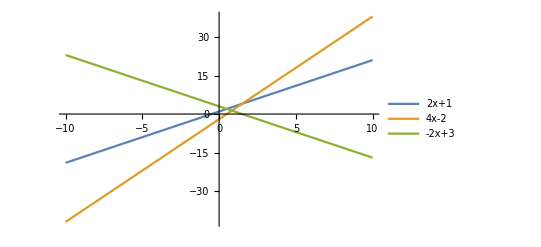

```mathematica
Plot[{2x+1,4x-2,-2x+3}, {x,-10,10},PlotLegends->Placed[{"2x+1","4x-2 ", "-2x+3"}, Above]]
(* Plotting some functions as example *)
```

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E1_CP_Q"],{EvaluationNotebook[], "E1_CP_Q"}]
```

### Comprensione guidata del parametro q

Partiamo cercando di capire cosa rappresenta il q della formula nei grafici :

```mathematica
Manipulate[Plot[2*x+ q ,{x,-3, +3},Epilog->{Red,PointSize@Large,Point[{0,Dynamic[q]}]},PlotRange->{10, -10},PlotLabel-> 2x+q],{q, -10,+10}, Row[{"Il valore attuale di q è  = " ,Dynamic[q]}]]
(* Plotting an example, TODO: Check if zoom function is correct *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia q?","Il termine noto q indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand]
 (* Creating a cliccable text *)
```

Hai dubbi su come cambia il grafico quando cambia q?

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E1_CP_Q0"],{EvaluationNotebook[], "E1_CP_Q0"}]
```

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando q = 0?

```mathematica
var ="" ;
Row[{Hyperlink[StatusArea[Button["Si"], "AG_C1_G1"],{EvaluationNotebook[], "AG_C1_G1"}],"\t",Button["No", If[p1== 0,var = Plot[2x, {x,-5,+5}, PlotLegends->"y = 2 x + 0"];
p1 = 1;
]]}] 


Dynamic[If[p1 === 1,  Plot[2x, {x,-5,+5}, PlotLegends-> Placed[{"y = 2 x + 0"}, Above],Epilog->{Red,PointSize@Large,Point[{0,0}]} ,ImageSize->Medium] Text["come puoi vedere la retta passa per l' origine"], Text[""]]]
```

No

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "AG_C1_G1"],{EvaluationNotebook[], "AG_C1_G1"}]
```

### Analisi guidata del coefficiente di primo grado

Ora abbiamo capito cosa vuol dire il termine noto sul grafico ma il coefficiente di primo grado m come si traduce sul grafico?

```mathematica
Manipulate[Plot[m*x-2 ,{x,-3, +3},PlotRange->{10, -10},PlotLabel-> m *x-2],{m, -10,+10}, Row[{"Il valore attuale di m è  = " ,Dynamic[m]}]]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia m?” ",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il coefficiente di primo grado indica l’inclinazione del grafico rispetto all’asse X"]}]
```

Hai dubbi su come cambia il grafico quando cambia m?”

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E1_CP_M"],{EvaluationNotebook[], "E1_CP_M"}]
```

### Comprensione del caso particolare

Hai notato cosa cambia se m < 0 o m > 0?

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "CP_1_A"],{EvaluationNotebook[], "CP_1_A"}],"\t",Button["No", p2 = 1]
}] 


Dynamic[If[p2 === 1,  Plot[{-x+2,x+2}, {x,-5,+5}, PlotLegends-> Placed[{"y = -x+2","y = x+2"}, Above], ImageSize->Medium]Text["Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0"], Text[""]]]
```

No

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "CP_1_A"],{EvaluationNotebook[], "CP_1_A"}]
```

### Comprensione del caso particolare

Hai notato cosa succede se m = 0?

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "CP_1_K"],{EvaluationNotebook[], "CP_1_K"}],"\t",Button["No", p3 = 1]
}] 


Dynamic[If[p3 === 1,  Plot[0x+1, {x,-5,+5}, PlotLegends-> Placed[{"0*X + 1"}, Above], ImageSize->Medium]Text["Come puoi vedere il grafico è parallelo all'asse X"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "CP_1_K"],{EvaluationNotebook[], "CP_1_K"}]
```

No

### Caso particolare x=k

Prima di farti sperimentare liberamente bisogna riflettere su un caso unico delle rette non delle funzioni.
Pensa a quale possa essere e poi scopriamolo insieme.


Il caso delle rette verticali che sono della forma x=k con k che è un qualunque numero.

```mathematica
Manipulate[ListLinePlot[{{k,10},{k,-10}},PlotRange->{{-4,+4},{-4,+4}},PlotLabel->StringJoin["x = ",ToString[k]]],{k,-3.5,3.5}]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "TS1"],{EvaluationNotebook[], "TS1"}]
```

### Ora tocca a te!

Inserisci tu le rette e osserva come sono rappresentate graficamente. Puoi confrontare contemporaneamente 5 funzioni polinomiali.

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq],String],Button["Confronta",If[Length[freeEq]<5   && !Quiet[ToExpression[currentEq]=== $Failed],AppendTo[freeEq,ToExpression[currentEq]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo o hai aggiunto caratteri speciali!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Manipulate[Plot[freeEq[[i]],{x,RangeSinistro, RangeDestro},PlotRange->Automatic,PlotLabel->freeEq[[i]], ImageSize->Medium],{RangeDestro, 10,100},{RangeSinistro,-10,-100} ,Row[{"x ha un intervallo che va da ", Dynamic[RangeDestro]," a " ,Dynamic[RangeSinistro]}]],"\t",Button["Elimina",freeEq=Delete[freeEq,Position[freeEq,freeEq[[i]]]]]}]],{i,Length[freeEq]}]]]}]]
(* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

Confronta

```mathematica
Row[{Print["Ti senti pronto per gli esercizi?"];Hyperlink[StatusArea[Button["Vai Esercizi"], "ES_G1"],{EvaluationNotebook[], "ES_G1"}],Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G1"],{EvaluationNotebook[], "E_G1"}]}]
```

Ti senti pronto per gli esercizi?

### Esercizi Tipologia 1

```mathematica
exKindAPrinter[1]
```

A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[1,1]] ===   0  || userAnswer[[1,2]] === 0 || userAnswer[[1,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[1]; clicked =1] ]]
```

```mathematica
Dynamic[If[clicked === 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G1_B"],{EvaluationNotebook[], "ES_G1_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[2]
```

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[2,1]] ===   0  || userAnswer[[2,2]] === 0 || userAnswer[[2,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[2];correctAnswerG1 =  correctCounter; clicked1b =1] ]]
```

```mathematica
Dynamic[If[clicked1b=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS1"],{EvaluationNotebook[], "RS1"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

## Risultati

```mathematica
Dynamic[If[correctAnswerG1  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG1]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG1]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G1"],{EvaluationNotebook[], "E_G1"}]}]
Button["Ricarica Esercizi", resetGrade[1, correctAnswerG1]; NotebookLocate["ES_G1"]](*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
(*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
Row[{Hyperlink[StatusArea[Button["Sezione Successiva"], "E_2G"],{EvaluationNotebook[], "E_2G"}]}]]
    Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}]
```

Funzioni polinomiali di 2 °Grado

### Introduzione

Le funzioni polinomiali di secondo grado hanno la forma y=ax^2+bx+c ovvero una parabola ma cosa vogliono dire i parametri a, b e c?

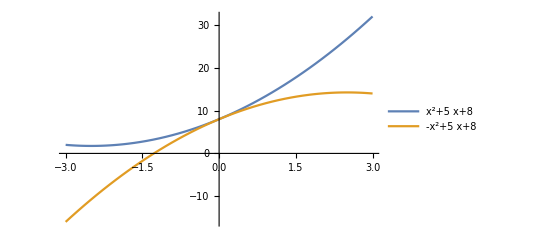

```mathematica
Plot[{1*x^2+5*x + 8, -1*x^2+5*x + 8 },{x,-3, +3}, PlotLegends->Placed[{1*x^2+5*x + 8, -1*x^2+5*x + 8 }, Above]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "CG_G2_PC"],{EvaluationNotebook[], "CG_G2_PC"}]
```

### Comprensione guidata del parametro c

Partiamo cercando di capire cosa rappresenta il c della formula:

```mathematica
Manipulate[Plot[4 x^2+ x+ c,{x,-3, +3},Epilog->{Green,PointSize@Large,Point[{0,Dynamic[c]}]},PlotRange->{10, -10}, PlotLabel-> x^2+ 2*x+ c],{c, -10,+10}, Row [{"L' attuale valore di c è :", Dynamic[c]}]]
(* Plotting an example *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia c?","il termine noto c indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E2_CP_C0"],{EvaluationNotebook[], "E2_CP_C0"}]
```

Hai dubbi su come cambia il grafico quando cambia c?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando c=0?

```mathematica
(*Row[{Hyperlink[StatusArea[Button["Si"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}],"\t",Button["No",If[p4== 0,p4=1;Print[Plot[x^2 +  2x, {x,-5,+5}, PlotLegends->"y = x^2 + 2x"]]; Print["Come puoi vedere il grafico passa per l' origine"]]]}] 
*)
Row[{Hyperlink[StatusArea[Button["Si"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}],"\t",Button["No", p4 = 1]
}] 


Dynamic[If[p4 === 1,  Plot[x^2 +  2x, {x,-5,+5},  PlotLegends->Placed[{x^2 +  2x}, Above],Epilog->{Green,PointSize@Large,Point[{0,0}]}, ImageSize -> Medium]Text["Come puoi vedere il grafico passa per l' origine"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}]
```

No

### Comprensione guidata del parametro b

Ma il parametro b come si traduce sul grafico?

```mathematica
Manipulate[Plot[-4 x^2+ b*x ,{x,-3, +3},PlotRange->{10, -10}, PlotLabel-> -4 x^2+ b*x, Epilog->{Green,PointSize@Large,Point[{Dynamic[b/8],Dynamic[b*b/16]}]}],{b, -10,+10}, Row[{"L' attuale valore di b è:", Dynamic[b]}]]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia b?","il coefficiente del termine di primo grado della X ha segno opposto ed e’ il doppio dell’ascissa del vertice della parabola",LinkHand] 
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E2_CP_B0"],{EvaluationNotebook[], "E2_CP_B0"}]
```

Hai dubbi su come cambia il grafico quando cambia b?

### Comprensione del caso particolare

Hai posto attenzione a cosa succede quando b=0?

```mathematica
(*Row[{Hyperlink[StatusArea[Button["Si"], "CG_G2_PB"],{EvaluationNotebook[], "CG_G2_PB"}],"\t",Button["No",If[p5== 0,p5=1;Print[Plot[x^2 +  1, {x,-5,+5}, PlotLegends->"y = x^2 + 1"]]; Print["come puoi vedere il grafico ha vertice sull’asse Y"]]]}] 
*)
Row[{Hyperlink[StatusArea[Button["Si"], "E_G2_CA"],{EvaluationNotebook[], "E_G2_CA"}],"\t",Button["No", p5 = 1]
}] 


Dynamic[If[p5 === 1, Plot[x^2 +  1, {x,-5,+5},PlotLegends->Placed[{x^2 +  1}, Above],Epilog->{Red,PointSize@Large,Point[{0,1}]} ,ImageSize -> Medium]Text["come puoi vedere il grafico ha vertice sull’asse Y"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E_G2_CA"],{EvaluationNotebook[], "E_G2_CA"}]
```

No

### Comprensione guidata del parametro a

cosa vuol dire graficamente il coefficiente a?

```mathematica
Manipulate[Plot[a*x^2 - 2*x  + 1,{x,-3, +3},PlotRange->{10, -10},PlotLabel->a* x^2 - 2*x + 1],{a, -10,+10}, Row[{"il varore attuale di a è :", Dynamic[a]}]]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia a?","il coefficiente del termine di secondo grado della X se positivo mi indica che la parabola e’ rivolta verso l’alto mentre se negativa e’ rivolta verso il basso.",LinkHand] 
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E2_CP_A0"],{EvaluationNotebook[], "E2_CP_A0"}]
```

Hai dubbi su come cambia il grafico quando cambia a?

### Caso particolare a = 0

Hai posto attenzione a cosa succede quando a=0?

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "TS2"],{EvaluationNotebook[], "TS2"}],"\t",Button["No", p6 = 1]}] 



Dynamic[If[p6 === 1, Plot[- 2x + 1, {x,-5,+5},PlotLegends->Placed[{- 2x + 1}, Above], ImageSize -> Medium]Text["come puoi vedere il grafico non e’ piu’ una parabola ma degenera in una retta"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E2_0"],{EvaluationNotebook[], "E2_0"}]
```

No

### Zeri di funzione

Per cercare gli zeri di una funzione polinomiale imponiamo f(x)=0 nel caso del 2° grado: ax^2+bx+c=0.

abbiamo 3 possibili risultati:

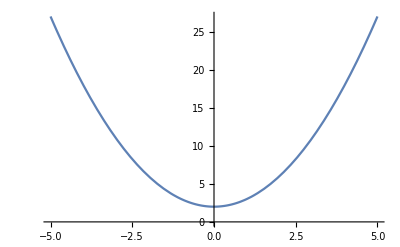

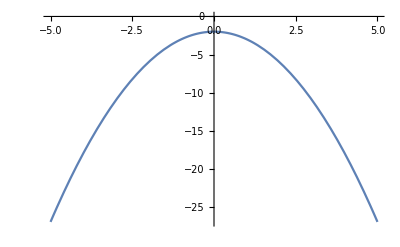

le parabole non intersecano mai l'asse x quindi entrambe non hanno zeri reali

le parabole intersecano l'asse x in un punto ma avvicinandosi molto all'asse x con un andamento curvo. in questo caso dico che ho uno zero doppio

le parabole intersecano l'asse x in due punti e il grafico delle parabole non si avvicina all'asse. In questo caso dico che ho uno zero semplice

```mathematica
Print[Plot[{x^2 +  2  }, {x,-5,+5}, PlotLegends->Placed[x^2 +  2 , Above]]]Print[Plot[{- x^2  - 2 }, {x,-5,+5}, PlotLegends->Placed[- x^2  - 2 , Above]]]; 
Print["le parabole non intersecano mai l'asse x quindi entrambe non hanno zeri reali"]
plotWithZoomButtons[x^2, Symbol["x"]]plotWithZoomButtons[-x^2, Symbol["x"]]
Print["le parabole intersecano l'asse x in un punto ma avvicinandosi molto all'asse x con un andamento curvo. in questo caso dico che ho uno zero doppio"]
plotWithZoomButtons[x^2 + x -3, Symbol["x"]]plotWithZoomButtons[-x^2 -x+3, Symbol["x"]]
Print["le parabole intersecano l'asse x in due punti e il grafico delle parabole non si avvicina all'asse. In questo caso dico che ho uno zero semplice"]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "TS2"],{EvaluationNotebook[], "TS2"}]
```

### Ora tocca a te!

Inserisci tu le parabole e osserva come sono rappresentate graficamente.Puoi confrontare contemporaneamente 5 equazioni

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq2],String],Button["Confronta",If[Length[freeEq2]<5 && !Quiet[ToExpression[currentEq2]=== $Failed],AppendTo[freeEq2,ToExpression[currentEq2]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo o hai inserito caratteri speciali!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Manipulate[Plot[freeEq2[[i]],{x,RangeSinistro, RangeDestro},PlotRange->Automatic,PlotLabel->freeEq2[[i]], ImageSize->Medium],{RangeDestro, 10,100},{RangeSinistro,-10,-100} ,Row[{"x ha un intervallo che va da ", Dynamic[RangeDestro]," a " ,Dynamic[RangeSinistro]}]],"\t",Button["Elimina",freeEq2=Delete[freeEq2,Position[freeEq2,freeEq2[[i]]]]]}]],{i,Length[freeEq2]}]]]}]]

(* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

Confronta

```mathematica
Row[{Print["Ti senti pronto per gli esercizi?"];Hyperlink[StatusArea[Button["Vai Esercizi"], "ES_G2"],{EvaluationNotebook[], "ES_G2"}],Hyperlink[StatusArea[Button["Torna alla teoria"], "E_2G"],{EvaluationNotebook[], "E_2G"}]}]
```

Ti senti pronto per gli esercizi?

### Esercizi Tipologia 1

```mathematica
exKindAPrinter[3]
```

A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[3,1]] ===   0  || userAnswer[[3,2]] === 0 || userAnswer[[3,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[3]; clicked2 =1] ]]
Dynamic[If[clicked2=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G2_B"],{EvaluationNotebook[], "ES_G2_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[4]
```

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[4,1]] ===   0  || userAnswer[[4,2]] === 0 || userAnswer[[4,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[4];correctAnswerG2=  correctCounter - correctAnswerG1; clicked2B =1] ]]
Dynamic[If[clicked2B=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS_G2"],{EvaluationNotebook[], "RS_G2"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Risultati

```mathematica
Dynamic[If[correctAnswerG2  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG2]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG2]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_2G"],{EvaluationNotebook[], "E_2G"}]}]
Button["Ricarica Esercizi", resetGrade[2, correctAnswerG2]; NotebookLocate["ES_G2"]]
Row[{Hyperlink[StatusArea[Button["Sezione Successiva"], "E_G3"],{EvaluationNotebook[], "E_G3"}]}]
Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}] (*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)

(*in questi due casi caso si chiama lu funzione che resetta i vettori nel package*)
```

Ricarica Esercizi

Funzioni polinomiali di 3 °Grado

### Introduzione

Le funzioni polinomiali di terzo grado hanno la forma y=ax^2+bx^2+cx+d ovvero una cubica ma cosa vogliono dire i parametri a, b, c e d?

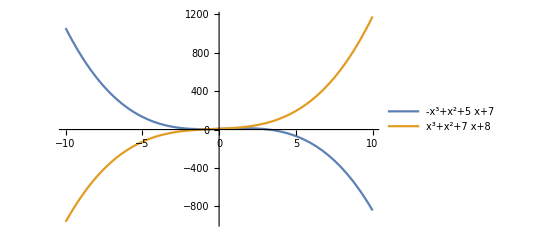

```mathematica
Plot[{-x^3+x ^2+5*x+ 7,x^3+x^2+7*x+ 8},{x,-10, 10},  PlotLegends->Placed[{-x^3+x ^2+5*x+ 7,x^3+x^2+7*x+ 8}, Above]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E_G3_CD"],{EvaluationNotebook[], "E_G3_CD"}]
```

### Comprensione guidata del parametro d

Partiamo cercando di capire cosa rappresenta il d della formula

```mathematica
Manipulate[Plot[2*x^3 +3*x^2+ x+ d,{x,-3, +3},PlotRange->{10, -10}, PlotLabel->x^3 + x^2+ 2*x+ d, Epilog->{Red,PointSize@Large,Point[{0,Dynamic[d]}]}],{d, -10,+10}, Row[{"Il valore attuale di d è:", Dynamic[d]}]]
(* Plotting an example *)
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia d?","il termine noto c indica l’ordinata del punto di intersezione del grafico con l’asse Y",LinkHand] 
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E3_CP_D0"],{EvaluationNotebook[], "E3_CP_D0"}]
```

Hai dubbi su come cambia il grafico quando cambia d?

### Caso particolare d = 0

Hai posto attenzione a cosa succede quando d=0?

```mathematica
(*Row[{Hyperlink[StatusArea[Button["Si"], "E_G3_CC"],{EvaluationNotebook[], "E_G3_CC"}],"\t",Button["No",If[p7== 0,p7=1;Print[Plot[2*x^3 +3*x^2+ x, {x,-5,+5}, PlotLegends->"y = 2*x^3 +3*x^2+ x"]]; Print["come puoi vedere il grafico passa  per l’origine"]]]}] 
*)
Row[{Hyperlink[StatusArea[Button["Si"], "E_G3_CC"],{EvaluationNotebook[], "E_G3_CC"}],"\t",Button["No", p7 = 1]
}] 


Dynamic[If[p7 === 1,Plot[2*x^3 +3*x^2+ x, {x,-5,+5},PlotLegends->Placed[{2*x^3 +3*x^2+ x}, Above], ImageSize -> Medium]Text["come puoi vedere il grafico passa  per l’origine"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E_G3_CC"],{EvaluationNotebook[], "E_G3_CC"}]
```

No

### Comprensione guidata del parametro c

Ma il parametro c come si traduce sul grafico?

```mathematica
Manipulate[Plot[2*x^3 +3*x^2+ c*x+ 1,{x,-3, +3}, PlotRange->{10, -10}, PlotLabel->2*x^3 +3*x^2+ c*x+ 1],{c, -10,+10}, Row[{"Il valore attuale di c è:", Dynamic[c]}]]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia c?","il coefficiente del termine di primo grado della x più è grande in valore assoluto più indica quanto il grafico assomiglia a una retta",LinkHand] 

Hyperlink[StatusArea[Import["img/right_arrow.png"], "E_G3_CB"],{EvaluationNotebook[], "E_G3_CB"}]
```

Hai dubbi su come cambia il grafico quando cambia c?

### Comprensione guidata parametro b

Ma il parametro b come si traduce sul grafico?

```mathematica
Manipulate[Plot[x^3 +b*x^2+ x+ 1,{x,-3, +3},PlotRange->{10, -10}, PlotLabel->x^3 + b * x^2+ x+ 1],{b, -10,+10}, Row[{"Il valore attuale di b è = "}, Dynamic[b]]]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia b?","il coefficiente del termine di secondo grado della x più è grande in valore assoluto più indica quanto il grafico nei suoi rami assomiglia a una parabola",LinkHand]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E_G3_CA"],{EvaluationNotebook[], "E_G3_CA"}]
```

Hai dubbi su come cambia il grafico quando cambia b?

### Comprensione guidata parametro a

cosa vuol dire graficamente il coefficiente a?

```mathematica
Manipulate[Plot[a*x^3 +4*x^2+ x+ 1,{x,-3, +3},PlotRange->{10, -10},PlotLabel->a* x^3 + 4* x^2+ x+ 1],{a, -10,+10}, Row[{"il valore attuale di a è =", Dynamic[a]}]]
```

```mathematica
hyperText["Hai dubbi su come cambia il grafico quando cambia a?","il coefficiente del termine di terzo grado della X indica quanto il grafico è pendente",LinkHand]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E3_CP_A"],{EvaluationNotebook[], "E3_CP_A"}]
```

Hai dubbi su come cambia il grafico quando cambia a?

### Caso particolare

Hai notato cosa cambia se a<0 o a>0?

```mathematica
(*Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}],"\t",Button["No",If[p8== 0,p8=1;Print[Plot[{x^3 + x^2+ x + 1, - x^3 + x^2+ x + 1}, {x,-10,+10}, PlotLabels-> "Expressions"]]; Print["come puoi vedere dai grafici se a>0 allora il grafico cresce al crescere delle X, se a<0 il grafico decresce al decrescere delle X"]]]}] 
*)
Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}],"\t",Button["No", p8 = 1]
}] 


Dynamic[If[p8 === 1,Plot[{x^3 + x^2+ x + 1, - x^3 + x^2+ x + 1}, {x,-10,+10},PlotLegends->Placed[{x^3 + x^2+ x + 1, - x^3 + x^2+ x + 1}, Above], ImageSize -> Medium]Text["come puoi vedere dai grafici se a>0 allora il grafico cresce al crescere delle X, se a<0 il grafico decresce al decrescere delle X"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}]
```

No

### Caso particolare a = 0

Hai posto attenzione a cosa succede quando a=0?

```mathematica
(*Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_A0"],{EvaluationNotebook[], "E3_CP_A0"}],"\t",Button["No",If[p9== 0,p9=1;Print[Plot[0*x^3 + 4*x^2+ x + 1, {x,-5,+5}, PlotLegends-> " 0*x^3 + 4*x^2+ x + 1"]]; Print["come puoi vedere il grafico non e’ piu’ una cubica ma degenera in una parabola"]]]}] 
*)

Row[{Hyperlink[StatusArea[Button["Si"], "E3_CP_0"],{EvaluationNotebook[], "E3_CP_0"}],"\t",Button["No", p9= 1]
}] 


Dynamic[If[p9 === 1,Plot[0*x^3 + 4*x^2+ x + 1, {x,-5,+5}, PlotLegends->Placed[{0*x^3 + 4*x^2+ x + 1}, Above], ImageSize -> Medium]Text["come puoi vedere il grafico non e’ piu’ una cubica ma degenera in una parabola"], Text[""]]]
Hyperlink[StatusArea[Import["img/right_arrow.png"], "E3_CP_0"],{EvaluationNotebook[], "E3_CP_0"}]
```

No

### Comprensione degli zeri

Analogamente al caso delle funzioni polimoniali di secondo grado poniamo: a*x^3 + b*x^2 + c*x + d = 0, abbiamo tre casi:
- Il caso con 3 zeri di funzioni semplice per i quali la funzione non si schiaccia sull’ asse X o il caso di un unico zero semplice :

```mathematica
plotWithZoomButtonsA[x^3 +3 x^2+ 4x, Symbol["x"]]plotWithZoomButtons[(x+ 1)*(x)*(x-1), Symbol["x"]]
```

Posso avere uno zero semplice e uno doppio (nel quale la funzione si schiaccia sull’ asse X come nel caso della parabola)

```mathematica
plotWithZoomButtonsB[x^3 +x^2, Symbol["x"]]
```

Infine abbiamo il caso di un zero triplo nel quale la funzione si schiaccia fortemente sull’ asse X cambiando di segno

```mathematica
plotWithZoomButtonsC[(x-4)^3 , Symbol["x"]]
```

```mathematica
Hyperlink[StatusArea[Import["img/right_arrow.png"], "TS3"],{EvaluationNotebook[], "TS3"}]
```

### Ora tocca a te!

ora tocca a puoi sperimentare. Inserisci tu le funzioni polinomiali e osserva come sono rappresentate graficamente. Puoi confrontarne contemporaneamente 5.

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq3],String],Button["Confronta",If[Length[freeEq3]<5 && !Quiet[ToExpression[currentEq3]=== $Failed] ,AppendTo[freeEq3,ToExpression[currentEq3]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo o hai inserito un carattere speciale!"],
MessageDialog[" hai inserito un carattere speciale!"]
]]}],Dynamic[Row[Table[With[{i=i},Column[{Manipulate[Plot[freeEq3[[i]],{x,RangeSinistro, RangeDestro},PlotRange->Automatic,PlotLabel->freeEq3[[i]], ImageSize->Medium],{RangeDestro, 10,100},{RangeSinistro,-10,-100} ,Row[{"x ha un intervallo che va da ", Dynamic[RangeDestro]," a " ,Dynamic[RangeSinistro]}]],"\t",Button["Elimina",freeEq3=Delete[freeEq3,Position[freeEq3,freeEq3[[i]]]]]}]],{i,Length[freeEq3]}]]]}]]


(* Drawing the list of the functions that the user want to compare, Delete button allow to remove that expression from the list; TODO Insert in package *)
```

Confronta

```mathematica
Row[{Print["Ti senti pronto per gli esercizi?"];Hyperlink[StatusArea[Button["Vai Esercizi"], "ES_G3"],{EvaluationNotebook[], "ES_G3"}],Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G3"],{EvaluationNotebook[], "E_G3"}]}]
```

Ti senti pronto per gli esercizi?

### Esercizi Tipologia 1

```mathematica
exKindAPrinter[5]
```

A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?


A quale funzione corrisponde la seguente retta?

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[5,1]] ===   0  || userAnswer[[5,2]] === 0 || userAnswer[[5,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[5]; clicked3 =1] ]]
Dynamic[If[clicked3=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"ES_G3_B"],{EvaluationNotebook[], "ES_G3_B"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Tipologia 2

```mathematica
exKindBPrinter[6]
```

```mathematica
Dynamic[Button["Verifica",If[userAnswer[[6,1]] ===   0  || userAnswer[[6,2]] === 0 || userAnswer[[6,3]] ===  0,  MessageDialog["Rispondi a tutte le domande prima di verificare"] , checkAnswer[6];correctAnswerG3 = correctCounter - correctAnswerG1 - correctAnswerG2 ; clicked3B =1] ]]
Dynamic[If[clicked3B=== 1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RS_G3"],{EvaluationNotebook[], "RS_G3"}], "Verifica la risposta prima di passare alla prossima sezione"]]
```

### Risultati

```mathematica
Dynamic[
If[correctAnswerG3  < 4, 
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG3]
Text["volendo puoi proseguire ma sarebbe meglio ripassare un po di teoria e poi riprovare gli esercizi"]
,
StringForm["Su 6 domande hai risposto correttamente a ``.",correctAnswerG3]
Text["hai compreso bene l’argomento ora puoi proseguire, ma se hai ancora qualche dubbio puoi comunque tornare indietro e riguardare le equazioni di primo grado"]
,
Text["Qualcosa è andato storto!!"]
]
Row[{Hyperlink[StatusArea[Button["Torna alla teoria"], "E_G3"],{EvaluationNotebook[], "E_G3"}]}] (*chiama funzione reset*)
Row[{Hyperlink[StatusArea[Button["Torna all' indice"], "Index"],{EvaluationNotebook[], "Index"}]}] 
Button["Ricarica Esercizi", resetGrade[3, correctAnswerG1]; NotebookLocate["ES_G3"]]
StringForm["Su 18 domande hai risposto correttamente a ``.",correctCounter]
]
```

```mathematica
""
NotebookLocate["Home"];
```